```mathematica
A0[g_, n_]:=2*√n*g;
cs0[g_,n_]:=Exp[-g^2/2]*Sum[(ⅈ*g)^(2*k)/(k!)^2*(n!)/((n-k)!),{k,0,Infinity}] ;
DT[Ω_]:=2 Pi/Ω;
BesselJ[0, 2 √n g];
SolN[g_,Ω_, n_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*y[t]),x[0]==0,y[0]==cs0[g, n], z[0]==0},{x,y,z},{t,0,1000}];
SolNcheck[g_,Ω_, n_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*y[t]),x[0]==0,y[0]==cs0[g, n], z[0]==0},{x,y,z},{t,0,1000}, InterpolationOrder->All, WorkingPrecision->40];
yy[g_,Ω_, n_]:=Evaluate[y[t]/.SolN[g,Ω,n][[1]]][[0]];
Mylist={};
g=2;
Ω=10;
nmax=40;
```

```mathematica
Setpoints={};
Setlines={};
Omegas={-10, -1,- 0.1};
cls={Red, Green, Blue};
For[omm=1,omm<4, omm++,s1={}; For[
n=0,
n<nmax,n++,a=yy[g,Omegas[[omm]], n];m=Mean[ParallelTable[a[t],{t,0,40, 40/2000}]];AppendTo[s1, {n,m}]];AppendTo[Setpoints,ListPlot[ s1, PlotStyle->cls[[omm]], PlotLegends->{Omegas[omm]}]];AppendTo[Setlines,ListPlot[ s1, Joined->True, PlotStyle->{Dashed, cls[[omm]]}]]]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

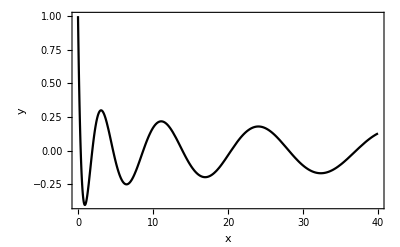
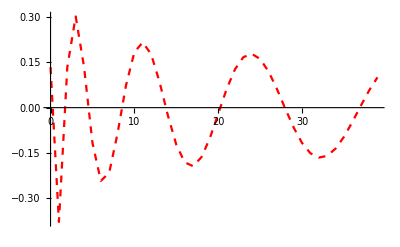
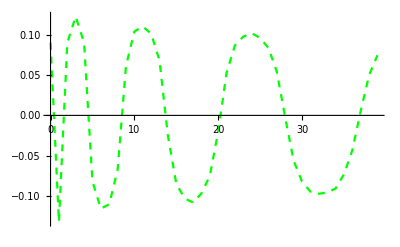
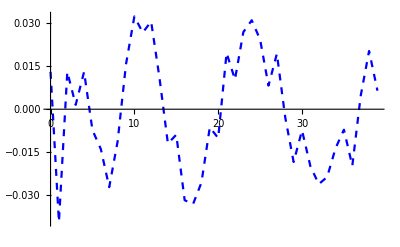
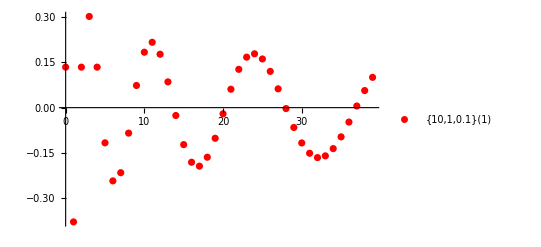
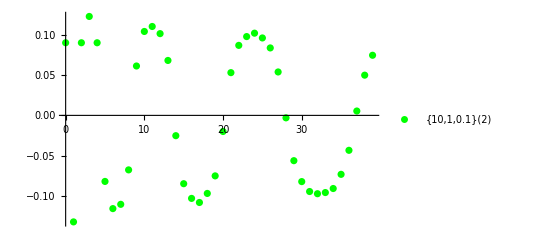
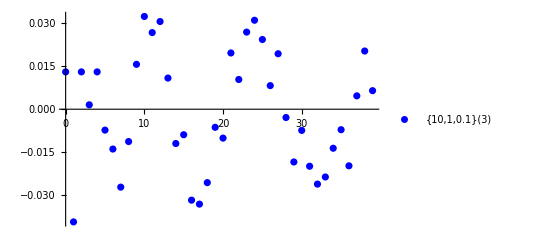
Show[-Graphics-,{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}]

```mathematica
p4=Plot[BesselJ[0,2*g*√n],{n,0,nmax}, Frame->True, PlotRange->All, PlotStyle->{Black}, AxesLabel->{"x","y"}];
Show[p4, Setlines,  Setpoints]
```

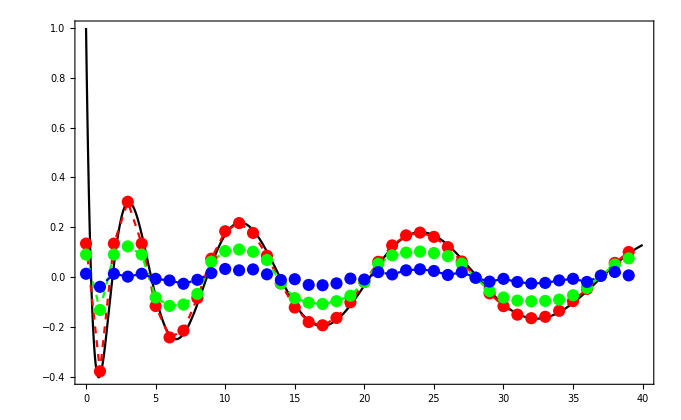

```mathematica
Show[%67,AxesLabel->{None,None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
PointLegend[{Red, Green, Blue}, {"Red", "Green", "Blue"}]
```

```mathematica
PointLegend[{Red,Green,Blue},{"Red","Green","Blue"}]
```

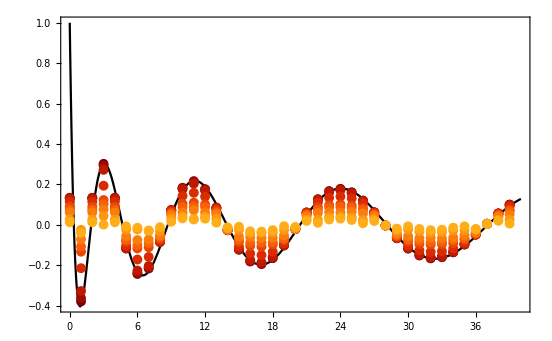

```mathematica
Show[%39,AxesLabel->{None,None},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

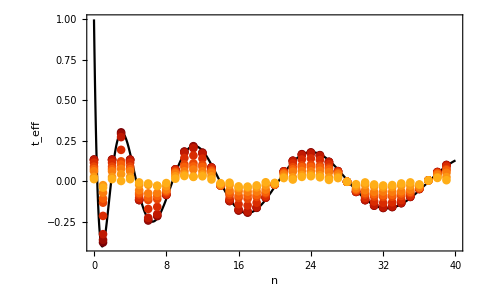

```mathematica
Show[%39,AxesLabel->{HoldForm["n"],HoldForm["t_eff"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
ColorData["SolarColors"]
```

ColorDataFunction[…]

```mathematica
BarLegend[{ColorData[{"SolarColors","Reverse"}],{0.1,1}}]
```

ColorDataFunction[…]

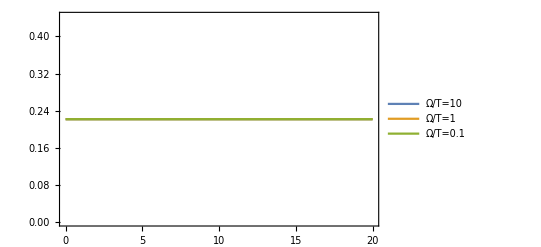

```mathematica
Plot[{Evaluate[y[t]/.SolN[2,-10,11]], Evaluate[y[t]/.SolN[2,-1,11]], Evaluate[y[t]/.SolN[2,-0.1,11]]},{t,0,20}, Frame->True, PlotLegends->{"Ω/T=10", "Ω/T=1", "Ω/T=0.1"}]
```

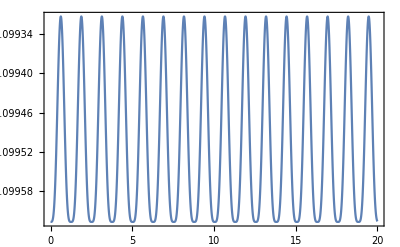

```mathematica
Plot[{Evaluate[y[t]/.SolN[1,5,20]]},{t,0,20}, Frame->True]
```

```mathematica
ND
```